```mathematica
ClearAll["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]]
dir=$HomeDirectory;
parse[data_]:={{#1,#2,#3},{#4,#5,#6},{#7,#8,#9}}&@@data;
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]]
```

Available:{plot2Doption,framelabel[xlabel_String,ylabel_String,size_:20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr}

Available:{plot2Doption,framelabel[xlabel_String,ylabel_String,size_:20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr}

### 面積分による精度確認

```mathematica
peaksFunction[x_,y_]:=3 (1-x)^2 Exp[-(x^2)-(y+1)^2]-10 (x/5-x^3-y^5) Exp[-x^2-y^2]-1/3 Exp[-(x+1)^2-y^2]
f[x_,y_]:=((*peaksFunction[x,y]**)Norm[Cross[D[{X,Y,peaksFunction[X,y]},X],D[{X,Y,D[peaksFunction[x,Y]]},Y]]])/.{Y->y,X->x}
NIntegrate[f[x,y],{x,-3.,3.},{y,-3.,3.}]
Plot3D[peaksFunction[x,y],{x,-3,3},{y,-3,3},
PlotRange->All,
(*PlotTheme->"Scientific",*)
BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->18],
AxesLabel->axeslabel[{"x","y","z"}],
ViewVector->{3*{3,-5,30},{0,0,0}},
Axes->True,
ImageSize->300,
BoxRatios->{1, 1, 1/3},
PlotTheme->"Classic"
]
```

114.096

-Graphics3D-

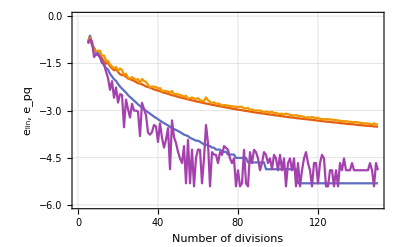
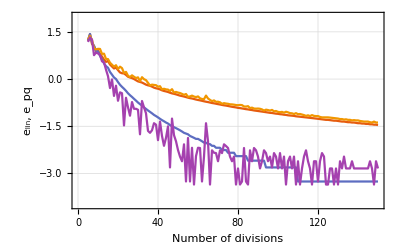
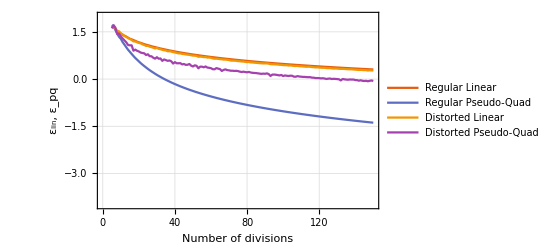

```mathematica
dir=$HomeDirectory;
id="_regular";
dataLinear=Import[FileNameJoin[{dir,"output","peaks_integral_linear"<>id<>".dat"}],"Data"];
dataPseudoQuad=Import[FileNameJoin[{dir,"output","peaks_integral_pseudo_quad"<>id<>".dat"}],"Data"];
dataOriginal=Import[FileNameJoin[{dir,"output","peaks_integral_original"<>id<>".dat"}],"Data"];
dataLinearError=Import[FileNameJoin[{dir,"output","peaks_integral_linear_error"<>id<>".dat"}],"Data"];
dataPseudoQuadError=Import[FileNameJoin[{dir,"output","peaks_integral_pseudo_quad_error"<>id<>".dat"}],"Data"];


id="_distorted";
dataLinearDistorted=Import[FileNameJoin[{dir,"output","peaks_integral_linear"<>id<>".dat"}],"Data"];
dataPseudoQuadDistorted=Import[FileNameJoin[{dir,"output","peaks_integral_pseudo_quad"<>id<>".dat"}],"Data"];
dataOriginalDistorted=Import[FileNameJoin[{dir,"output","peaks_integral_original"<>id<>".dat"}],"Data"];
dataLinearDistortedError=Import[FileNameJoin[{dir,"output","peaks_integral_linear_error"<>id<>".dat"}],"Data"];
dataPseudoQuadDistortedError=Import[FileNameJoin[{dir,"output","peaks_integral_pseudo_quad_error"<>id<>".dat"}],"Data"];


trueIntegral=114.09555552416919;
Row@{
fig0=ListPlot[
{{#1,Log10[Norm[(trueIntegral-#2)/trueIntegral]]}&@@@dataLinear,
{#1,Log10[Norm[(trueIntegral-#2)/trueIntegral]]}&@@@dataPseudoQuad,
(*{#1,#2}&@@@dataOriginal,*)
{#1,Log10[Norm[(trueIntegral-#2)/trueIntegral]]}&@@@dataLinearDistorted,
{#1,Log10[Norm[(trueIntegral-#2)/trueIntegral]]}&@@@dataPseudoQuadDistorted}
,GridLines->Automatic
,FrameLabel->framelabel["Number of divisions","e_lin, e_pq"]
,PlotRange->{Automatic,{-6,0}}
,Evaluate[plot2Doption]
,Epilog->{Line[{{0,trueIntegral},{100,trueIntegral}}]}
],
fig1=ListPlot[
{{#1,Log10@Norm[trueIntegral-#2]}&@@@dataLinear,
{#1,Log10@Norm[trueIntegral-#2]}&@@@dataPseudoQuad,
(*{#1,#2}&@@@dataOriginal,*)
{#1,Log10@Norm[trueIntegral-#2]}&@@@dataLinearDistorted,
{#1,Log10@Norm[trueIntegral-#2]}&@@@dataPseudoQuadDistorted}
,GridLines->Automatic
,FrameLabel->framelabel["Number of divisions","e_lin, e_pq"]
,PlotRange->{Automatic,{-4,2}}
,Evaluate[plot2Doption]
,Epilog->{Line[{{0,trueIntegral},{100,trueIntegral}}]}
],
fig2=ListPlot[
{{#1,Log10@#2}&@@@dataLinearError,
{#1,Log10@#2}&@@@dataPseudoQuadError,
{#1,Log10@#2}&@@@dataLinearDistortedError,
{#1,Log10@#2}&@@@dataPseudoQuadDistortedError}
,GridLines->Automatic
,PlotLegends->Placed[{"Regular Linear","Regular Pseudo-Quad","Distorted Linear","Distorted Pseudo-Quad"},Right]
,PlotRange->{Automatic,{-4,2}}
,FrameLabel->framelabel["Number of divisions","ε_lin, ε_pq"]
,Evaluate[plot2Doption]
,Epilog->{Line[{{0,trueIntegral},{100,trueIntegral}}]}
]}
```

```mathematica
(*toFit[d_]:=d^(1.2)*)


Manipulate[
Module[{},
toFit1[d_]:=(d-sa)^(a)+sa;
toFit2[d_]:=(d-sb)^(b)+sb;
(*toFit[d_]:=d*)
Row@{
ListPlot[
{{#1,Log10@#2}&@@@dataLinearError,
{#1,Log10@#2}&@@@dataPseudoQuadError,
{#1,Log10@#2}&@@@dataLinearDistortedError,
{#1,Log10@#2}&@@@dataPseudoQuadDistortedError,
{toFit1@#1,Log10@#2}&@@@dataPseudoQuadError,
{toFit2@#1,Log10@#2}&@@@dataPseudoQuadDistortedError}
,PlotRange->{{0,150},{-1,2}}
,PlotLabel->{"a",a,"b",b,"sa",sa,"sb",sb}
,Evaluate[plot2Doption]
,Epilog->{Line[{{0,trueIntegral},{100,trueIntegral}}]}
]}
],{a,1.64,2.,0.01},{b,1.2,2.,0.01},{sa,6,30,1},{sb,0,30,1}
]
```

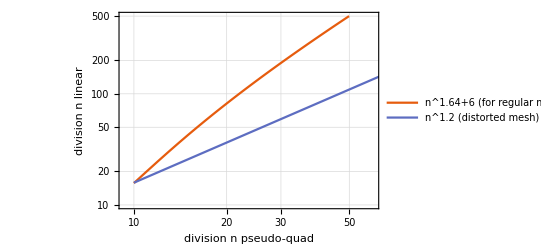

```mathematica
ListLogLogPlot[
{Table[{npseudo,(npseudo-6)^(1.64)+6} ,{npseudo,10,100,1}],
Table[{npseudo,(npseudo)^(1.2)} ,{npseudo,10,100,1}](*,
Table[{npseudo,2.*(npseudo)} ,{npseudo,10,100,1}]*)}
,PlotLegends->{"n^1.64+6 (for regular mesh)","n^1.2 (distorted mesh)"}
,PlotRange->{{0,60},{10,500}}
,Evaluate[plot2Doption]
,GridLines->All
,FrameLabel->framelabel["division n pseudo-quad","division n linear"]
]
```